## About this program

Tested on the Mathematica version 14.3.
If you use this code in academic work, please cite: “E. Ievlev, M. Shifman, Degenerate kinks and kink-instantons in two-dimensional scalar field models with N=1 and N=2 supersymmetry, arXiv:2509.14324 [hep-th].”
Equation and Section numbers refer to the paper above.

## Some preparatory definitions

```mathematica
(* Autosave after every execution *)
(*CurrentValue[$FrontEnd,"NotebookAutoSave"]=True*)
```

```mathematica
(* Do not use Csch, Sech https://mathematica.stackexchange.com/a/7800 *)
$PrePrint=#/. {Csch[z_]:>1/Defer@Sinh[z],Sech[z_]:>1/Defer@Cosh[z]}&;
```

```mathematica
(* Set up a directory for saving files *)
With[{dirname=FileNameJoin[{NotebookDirectory[],"data"}]},
Switch[FileType[dirname],
None,CreateDirectory[dirname] (*create dir*),
Directory,Null (*do nothing*),
File,Print["File with same name already exists!"] (*error!*)]];
(* Set the directory "/data" as a default directory *)
SetDirectory[FileNameJoin[{NotebookDirectory[],"data"}]];
```

## ADS - motivated model

### Preliminaries

```mathematica
(* (super) potential *)
W=a/Φ+b*Φ
dW=D[W,Φ]
V=Abs[dW]^2
Vreal=V/.{Φ->X+I*Y}//ComplexExpand//Simplify
```

a/Φ+b Φ

b-a/Φ^2

Abs[b-a/Φ^2]^2

(a^2+2 a b (-X^2+Y^2)+b^2 (X^2+Y^2)^2)/((X^2+Y^2)^2)

```mathematica
(* Vacua *)
Vac=Φ/.Solve[dW==0,Φ]
```

{-(√a)/(√b),(√a)/(√b)}

```mathematica
Wvac1=W/.{Φ->Vac[[1]]}//Simplify
Wvac2=W/.{Φ->Vac[[2]]}//Simplify
```

-2 √a √b

2 √a √b

```mathematica
(* Perturbative mass *)
fields={X,Y};
MassMat=Table[Table[1/2*D[Vreal,f1,f2]//Simplify,{f1,fields}],{f2,fields}]; (* Note the 1/2, because there is no 1/2 in the kinetic term, and we differentiate over the real fields *)
MassMatVac=MassMat/.{X->Vac[[2]],Y->0}//Simplify;
MassMatVac//MatrixForm
MassClassical=Sqrt[MassMatVac[[1]][[1]]]
```

((4 b^3)/a | 0
0 | (4 b^3)/a)

2 √(b^3/a)

```mathematica
(* See what happens in the middle of a kink *)
MassMatKink=MassMat/.{X->0,Y->Vac[[2]]}//Simplify;
MassMatKink//MatrixForm
```

(-(8 b^3)/a | 0
0 | (16 b^3)/a)

### BPS kinks

```mathematica
(* Kink profiles *)
theta=2*ArcTan[Exp[-MassClassical*z]]
Φkink=Vac[[2]]*Exp[I*theta]
Φkink=FullSimplify[ComplexExpand[Φkink,TargetFunctions->{Re,Im}],Assumptions->{b>0,a>0,z>0}]
```

2 ArcTan[ⅇ^(-2 √(b^3/a) z)]

(√a ⅇ^(2 ⅈ ArcTan[ⅇ^(-2 √(b^3/a) z)]))/(√b)

√(a/b) (1+(2 ⅈ)/(-ⅈ+ⅇ^((2 b^(3/2) z)/(√a))))

```mathematica
Xkink=FullSimplify[ComplexExpand[Re[Φkink],TargetFunctions->{Re,Im}],Assumptions->{b>0,a>0,z>0}]
Ykink=FullSimplify[ComplexExpand[Im[Φkink],TargetFunctions->{Re,Im}],Assumptions->{b>0,a>0,z>0}]
```

√(a/b) Tanh[(2 b^(3/2) z)/(√a)]

(√(a/b))/Cosh[(2 b^(3/2) z)/(√a)]

```mathematica
(* Check different representation for the kink *)
ΦkinkAlt=Vac[[2]]*(Exp[MassClassical*z]+I)/(Exp[MassClassical*z]-I)
Print["Next output should be zero (alt. forms for kink):"]
FullSimplify[ΦkinkAlt-Φkink//ComplexExpand,Assumptions->{b>0,a>0,Element[z,Reals]}]
```

(√a (ⅈ+ⅇ^(2 √(b^3/a) z)))/(√b (-ⅈ+ⅇ^(2 √(b^3/a) z)))

Next output should be zero (alt. forms for kink):

0

#### theta form

```mathematica
(* Check mass *)
(*Limit[theta/Exp[-MassClassical*z],z->+Infinity]
Limit[theta/Exp[+MassClassical*z],z->-Infinity]*)
thetaPlus=Simplify[theta/.{z->-1/MassClassical*Log[t]},Assumptions->{b>0,a>0,t>0}];
Series[thetaPlus,{t,0,2}]

thetaMinus=Simplify[theta/.{z->1/MassClassical*Log[t]},Assumptions->{b>0,a>0,t>0}];
Simplify[Series[thetaMinus,{t,0,2}],Assumptions->{b>0,a>0,t>0}]
```

2 t+O[t]^3

π-2 t+O[t]^3

```mathematica
(* Check the BPS equation for theta *)
lhs=D[theta,z];
rhs=-2*b^(3/2)/a^(1/2)*Sin[theta];
Print["Next output should be zero (BPS equation):"]
FullSimplify[lhs-rhs,Assumptions->{a>0,b>0}]
```

Next output should be zero (BPS equation):

0

#### Φ form

```mathematica
(* Check mass *)
ΦPlus=Simplify[Φkink/.{z->-1/MassClassical*Log[t]},Assumptions->{b>0,a>0,t>0}];
Series[ΦPlus,{t,0,2}]

ΦMinus=Simplify[Φkink/.{z->1/MassClassical*Log[t]},Assumptions->{b>0,a>0,t>0}];
Simplify[Series[ΦMinus,{t,0,2}],Assumptions->{b>0,a>0,t>0}]
```

√(a/b)+2 ⅈ √(a/b) t-2 √(a/b) t^2+O[t]^3

-√(a/b)+2 ⅈ √(a/b) t+2 √(a/b) t^2+O[t]^3

```mathematica
(* Check the BPS equation for Φ *)
lhs=FullSimplify[ComplexExpand[D[Φkink,z],TargetFunctions->{Re,Im}],Assumptions->{b>0,a>0,z>0}]
rhs=FullSimplify[ComplexExpand[Conjugate[dW/.{Φ->Φkink}],TargetFunctions->{Re,Im}],Assumptions->{b>0,a>0,z>0}]
Print["One of the next outputs should be zero (BPS equation):"]
FullSimplify[ComplexExpand[lhs+rhs,TargetFunctions->{Re,Im}],Assumptions->{b>0,a>0,z>0}]
FullSimplify[ComplexExpand[lhs-rhs,TargetFunctions->{Re,Im}],Assumptions->{b>0,a>0,z>0}]
```

(2 b)/(1+ⅈ Sinh[(2 b^(3/2) z)/(√a)])

(2 b)/(1+ⅈ Sinh[(2 b^(3/2) z)/(√a)])

One of the next outputs should be zero (BPS equation):

-(4 ⅈ b)/(-ⅈ+Sinh[(2 b^(3/2) z)/(√a)])

0

```mathematica
(* Check the BPS equation for \bar[Φ] *)
Φdkink=Conjugate[Φkink];
lhs=FullSimplify[ComplexExpand[D[Φdkink,z],TargetFunctions->{Re,Im}],Assumptions->{b>0,a>0,z>0}]
rhs=FullSimplify[ComplexExpand[Conjugate[dW/.{Φ->Φdkink}],TargetFunctions->{Re,Im}],Assumptions->{b>0,a>0,z>0}]
Print["One of the next outputs should be zero (BPS equation):"]
FullSimplify[ComplexExpand[lhs+rhs,TargetFunctions->{Re,Im}],Assumptions->{b>0,a>0,z>0}]
FullSimplify[ComplexExpand[lhs-rhs,TargetFunctions->{Re,Im}],Assumptions->{b>0,a>0,z>0}]
```

(2 ⅈ b)/(ⅈ+Sinh[(2 b^(3/2) z)/(√a)])

(2 ⅈ b)/(ⅈ+Sinh[(2 b^(3/2) z)/(√a)])

One of the next outputs should be zero (BPS equation):

(4 ⅈ b)/(ⅈ+Sinh[(2 b^(3/2) z)/(√a)])

0

### Sphaleron

```mathematica
(* Integrate the BPS equation, assuming Φ is real *)
zsphaleron=Integrate[-1/dW,Φ]
```

-Φ/b+(√a ArcTanh[(√b Φ)/(√a)])/b^(3/2)

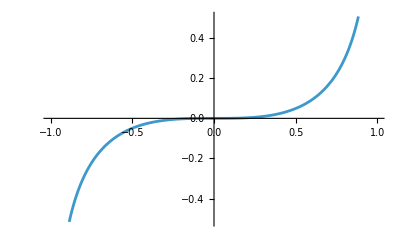

```mathematica
Plot[zsphaleron/.{a->1,b->1},{Φ,-1,1}]
```

```mathematica
(* Behavior near the origin *)
Series[zsphaleron,{Φ,0,4}]
```

Φ^3/(3 a)+O[Φ]^5

## Instanton

### BPS equation in different forms

#### Cartesian coordinates in Euclidean spacetime

```mathematica
(* Field Φ, coordinates Cartesian representation *)
InstEqΦzt=(D[Φ[z,t],z]-I*D[Φ[z,t],t])-Conjugate[dW/.{Φ->Φ[z,t]}]
```

-Conjugate[b-a/Φ[z,t]^2]-ⅈ Φ^(0,1)[z,t]+Φ^(1,0)[z,t]

```mathematica
(* Field Cartesian, coordinates Cartesian representation *)
InstEqXYzt=InstEqΦzt/.{Φ->Function[{z,t},X[z,t]+I*Y[z,t]]}//ComplexExpand//Simplify;
InstEqXYzt1=Re[InstEqXYzt]//ComplexExpand//FullSimplify
InstEqXYzt1=Im[InstEqXYzt]//ComplexExpand//FullSimplify
```

-b+(a (X[z,t]^2-Y[z,t]^2))/((X[z,t]^2+Y[z,t]^2)^2)+Y^(0,1)[z,t]+X^(1,0)[z,t]

(2 a X[z,t] Y[z,t])/((X[z,t]^2+Y[z,t]^2)^2)-X^(0,1)[z,t]+Y^(1,0)[z,t]

```mathematica
(* Field polar, coordinates Cartesian representation *)
InstEqΥθzt=InstEqΦzt/.{Φ->Function[{z,t},Υ[z,t]*Exp[I*θ[z,t]]]}//ComplexExpand//Simplify;
InstEqΥθzt1=Re[InstEqΥθzt]*Cos[θ[z,t]]+Im[InstEqΥθzt]*Sin[θ[z,t]]//ComplexExpand//FullSimplify
InstEqΥθzt2=Re[InstEqΥθzt]*Sin[θ[z,t]]-Im[InstEqΥθzt]*Cos[θ[z,t]]//ComplexExpand//FullSimplify
```

-b Cos[θ[z,t]]+(a Cos[θ[z,t]])/Υ[z,t]^2+Υ[z,t] θ^(0,1)[z,t]+Υ^(1,0)[z,t]

-b Sin[θ[z,t]]-(a Sin[θ[z,t]])/Υ[z,t]^2+Υ^(0,1)[z,t]-Υ[z,t] θ^(1,0)[z,t]

#### Polar coordinates in Euclidean spacetime

```mathematica
(* Check of the cartesian-polar relation for derivatives *)
MyFunc1=z^2*t^4+I*Cos[z/2]*t^10
MyFunc2=MyFunc1/.{z->r*Cos[α],t->r*Sin[α]}//Simplify
difference=(D[MyFunc1,z]-I*D[MyFunc1,t])-Exp[-I*α]*(D[MyFunc2,r]-I/r*D[MyFunc2,α]);
Print["Next output should be zero (simple equivalence check):"]
FullSimplify[ComplexExpand[difference/.{z->r*Cos[α],t->r*Sin[α]},TargetFunctions->{Re,Im}],Assumptions->{r>0,Element[α,Reals]}]
```

t^4 z^2+ⅈ t^10 Cos[z/2]

r^6 Sin[α]^4 (Cos[α]^2+ⅈ r^4 Cos[1/2 r Cos[α]] Sin[α]^6)

Next output should be zero (simple equivalence check):

0

```mathematica
(* Field Φ, coordinates polar representation *)
InstEqΦrα=Exp[-I*α]*(D[Φ[r,α],r]-I/r*D[Φ[r,α],α])-Conjugate[dW/.{Φ->Φ[r,α]}]
```

-Conjugate[b-a/Φ[r,α]^2]+ⅇ^(-ⅈ α) (-(ⅈ Φ^(0,1)[r,α])/r+Φ^(1,0)[r,α])

```mathematica
(* Field Cartesian, coordinates polar representation *)
InstEqXYrα=InstEqΦrα/.{Φ->Function[{r,α},X[r,α]+I*Y[r,α]]}//ComplexExpand//Simplify;
InstEqXYrα1=Re[InstEqXYrα]*Sin[α]+Im[InstEqXYrα]*Cos[α]//ComplexExpand//FullSimplify
InstEqXYrα1=Re[InstEqXYrα]*Cos[α]-Im[InstEqXYrα]*Sin[α]//ComplexExpand//FullSimplify
```

-b Sin[α]+(a (2 Cos[α] X[r,α] Y[r,α]+Sin[α] (X[r,α]^2-Y[r,α]^2)))/((X[r,α]^2+Y[r,α]^2)^2)-(X^(0,1)[r,α])/r+Y^(1,0)[r,α]

-b Cos[α]+(a (-2 Sin[α] X[r,α] Y[r,α]+Cos[α] (X[r,α]^2-Y[r,α]^2)))/((X[r,α]^2+Y[r,α]^2)^2)+(Y^(0,1)[r,α])/r+X^(1,0)[r,α]

```mathematica
(* Field polar, coordinates polar representation *)
InstEqΥθrα=InstEqΦrα/.{Φ->Function[{r,α},Υ[r,α]*Exp[I*θ[r,α]]]}//ComplexExpand//Simplify;
InstEqΥθrα1=Re[InstEqΥθrα]*Cos[α-θ[r,α]]-Im[InstEqΥθrα]*Sin[α-θ[r,α]]//ComplexExpand//Simplify
InstEqΥθrα2=Re[InstEqΥθrα]*Sin[α-θ[r,α]]+Im[InstEqΥθrα]*Cos[α-θ[r,α]]//ComplexExpand//Simplify
```

-b Cos[α-θ[r,α]]+(a Cos[α+θ[r,α]])/Υ[r,α]^2+(Υ[r,α] θ^(0,1)[r,α])/r+Υ^(1,0)[r,α]

(a Sin[α+θ[r,α]])/Υ[r,α]^2-(b r Sin[α-θ[r,α]]+Υ^(0,1)[r,α])/r+Υ[r,α] θ^(1,0)[r,α]

#### Check near the singularity

```mathematica
(* Leading singularity in the BPS equation cancels *)
SingSub={Υ->Function[{r,α},(3/2*a*r)^(1/3)],θ->Function[{r,α},-α]};
InstEqΥθrα1/.SingSub//Simplify
InstEqΥθrα2/.SingSub//Simplify
```

-b Cos[2 α]

-b Sin[2 α]

### Classical action

```mathematica
LagrΦzt=Abs[D[Φ[z,t],z]]^2+Abs[D[Φ[z,t],t]]^2+Abs[dW/.{Φ->Φ[z,t]}]^2
```

Abs[b-a/Φ[z,t]^2]^2+Abs[Φ^(0,1)[z,t]]^2+Abs[Φ^(1,0)[z,t]]^2

```mathematica
LagrXYzt=LagrΦzt/.{Φ->Function[{z,t},X[z,t]+I*Y[z,t]]}//ComplexExpand//Simplify
```

b^2+(a^2 X[z,t]^4)/((X[z,t]^2+Y[z,t]^2)^4)+(a^2 Y[z,t]^4)/((X[z,t]^2+Y[z,t]^2)^4)+(2 a b Y[z,t]^2)/((X[z,t]^2+Y[z,t]^2)^2)+(2 a X[z,t]^2 (a Y[z,t]^2-b (X[z,t]^2+Y[z,t]^2)^2))/((X[z,t]^2+Y[z,t]^2)^4)+(X^(0,1)[z,t])^2+(Y^(0,1)[z,t])^2+(X^(1,0)[z,t])^2+(Y^(1,0)[z,t])^2

### Integrating the singular asymptotics

```mathematica
LagrXYztSimple=LagrXYzt/.{a->1,b->1}//Simplify
XinstVar=(3/2)^(1/3)*z/(z^2+t^2)^(1/3)
YinstVar=(3/2)^(1/3)*(-t)/(z^2+t^2)^(1/3)
LagrXYztinst=LagrXYztSimple/.{X->Function[{z,t},XinstVar],Y->Function[{z,t},YinstVar]}//Simplify
```

1+X[z,t]^4/((X[z,t]^2+Y[z,t]^2)^4)+Y[z,t]^4/((X[z,t]^2+Y[z,t]^2)^4)+(2 Y[z,t]^2)/((X[z,t]^2+Y[z,t]^2)^2)+(2 X[z,t]^2 (Y[z,t]^2-(X[z,t]^2+Y[z,t]^2)^2))/((X[z,t]^2+Y[z,t]^2)^4)+(X^(0,1)[z,t])^2+(Y^(0,1)[z,t])^2+(X^(1,0)[z,t])^2+(Y^(1,0)[z,t])^2

((3/2)^(1/3) z)/((t^2+z^2)^(1/3))

-((3/2)^(1/3) t)/((t^2+z^2)^(1/3))

1/(9 (t^2+z^2)^(5/3))(z^2 (2 2^(1/3) 3^(2/3)-6 2^(2/3) 3^(1/3) (t^2+z^2)^(1/3)+9 (t^2+z^2)^(2/3))+t^2 (2 2^(1/3) 3^(2/3)+6 2^(2/3) 3^(1/3) (t^2+z^2)^(1/3)+9 (t^2+z^2)^(2/3)))

```mathematica
LagrXYrαinst=Simplify[LagrXYztinst/.{z->r*Cos[α],t->r*Sin[α]},Assumptions->{r>0}]
LagrXYrinst=Integrate[LagrXYrαinst,{α,0,2*Pi}]
Sinst=Integrate[r*LagrXYrinst,{r,0,R}]
```

1+(2 (2/3)^(1/3))/(3 r^(4/3))-(2 (2/3)^(2/3) Cos[2 α])/r^(2/3)

π (2+(4 (2/3)^(1/3))/(3 r^(4/3)))

π (2 (2/3)^(1/3) R^(2/3)+R^2)

## Phi-4 (N=2) model in real (N=1) formulation

```mathematica
Wphi4complex=m^2/(4*λ)*Φ-λ/3*Φ^3/.{Φ->X+I*Y}
Wphi4real=Im[Wphi4complex]//ComplexExpand
```

(m^2 (X+ⅈ Y))/(4 λ)-1/3 (X+ⅈ Y)^3 λ

(m^2 Y)/(4 λ)-X^2 Y λ+(Y^3 λ)/3

```mathematica
WX=D[Wphi4real,X]//Simplify
WY=D[Wphi4real,Y]//Simplify
Solve[{WX==0,WY==0},{X,Y},Reals]
```

-2 X Y λ

m^2/(4 λ)+(-X^2+Y^2) λ

{{X→-1/2 √(m^2/λ^2),Y→0},{X→1/2 √(m^2/λ^2),Y→0}}

```mathematica
fields={X,Y};
MassMat=Table[Table[D[Wphi4real,f1,f2]//Simplify,{f1,fields}],{f2,fields}];
MassMat//MatrixForm
MassEigSys=Eigensystem[MassMat]
```

(-2 Y λ | -2 X λ
-2 X λ | 2 Y λ)

{{-2 √(X^2+Y^2) λ,2 √(X^2+Y^2) λ},{{-(-Y-√(X^2+Y^2))/X,1},{-(-Y+√(X^2+Y^2))/X,1}}}

```mathematica
(* Note: slightly unconventional angle *)
MassEigVal=FullSimplify[MassEigSys[[1]]/.{X->R*Sin[t],Y->R*Cos[t]},Assumptions->{R>0}]
MassEigVec=FullSimplify[MassEigSys[[2]]*X/.{X->R*Sin[t],Y->R*Cos[t]},Assumptions->{R>0}];
MassEigVec[[1]]/(2*R*Cos[t/2])//Simplify
MassEigVec[[2]]/(2*R*Sin[t/2])//Simplify
```

{-2 R λ,2 R λ}

{Cos[t/2],Sin[t/2]}

{-Sin[t/2],Cos[t/2]}

```mathematica
(* There is a solution for Dpsi=0 as well as D^dagger psi = 0, because of two flavors *)
Eigensystem[MassMat/.{X->-1,Y->0}]
Eigensystem[MassMat/.{X->+1,Y->0}]
```

{{-2 λ,2 λ},{{-1,1},{1,1}}}

{{-2 λ,2 λ},{{1,1},{-1,1}}}